# Wavelet Proposal

## Haar wavelets

```mathematica
P=Piecewise[{{-1, 1/2<x<1}, {1, 0<x<1/2}}]
```

Piecewise[{{-1, 1/2<x<1}, {1, 0<x<1/2}, {0, True}}]

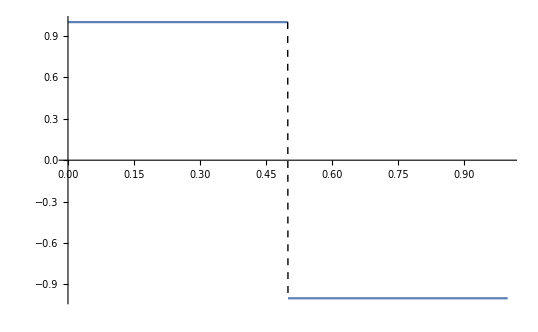

```mathematica
p1 = Plot[P,{x,0,1}, ExclusionsStyle->Dashed]
```

Piecewise[{{-1, 3/2<x<2}, {1, 1<x<3/2}, {0, True}}]

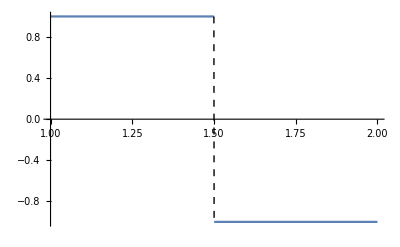

```mathematica
P01=Piecewise[{{-1, 1+1/2<x<1+1}, {1, 1<x<1+1/2}}]
p01 = Plot[P01,{x,1,2}, ExclusionsStyle->Dashed]
```

```mathematica
P01=Piecewise[{{-1, 1+1/2<x<1+1}, {1, 1<x<1+1/2}}]
p01 = Plot[P01,{x,1,2}, ExclusionsStyle->Dashed]
```

```mathematica
P01=Piecewise[{{-1, 1+1/2<x<1+1}, {1, 1<x<1+1/2}}]
p01 = Plot[P01,{x,1,2}, ExclusionsStyle->Dashed]
```

Piecewise[{{-1, 3/2<x<2}, {1, 1<x<3/2}, {0, True}}]

Plot::nonopt: Options expected (instead of Thickness[r]) beyond position 2 in Plot[P01,{x,1,2},ExclusionsStyle→Dashed,Thickness[r]]. An option must be a rule or a list of rules.

Plot[P01,{x,1,2},ExclusionsStyle→Dashed,Thickness[r]]

Piecewise[{{-1, 15/16<x<1}, {1, 7/8<x<15/16}, {0, True}}]

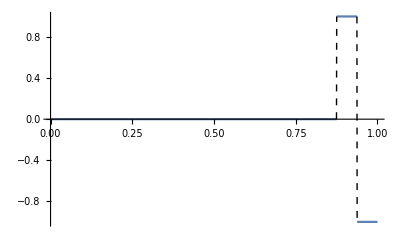

```mathematica
P34=Piecewise[{{-1, (1/2+7)/8<x<1}, {1, 7/8<x<(1/2+7)/8}}]
p34 = Plot[P34,{x,0,1}, ExclusionsStyle->Dashed]
```

```mathematica
Show[p1,p01,h1,PlotRange->All]
```

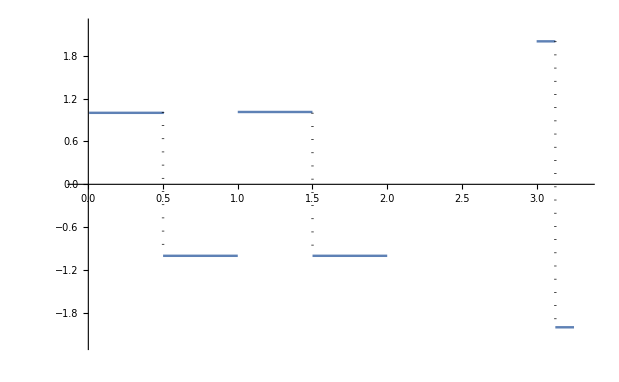

```mathematica
N[2^(3/2)]
```

2.82843

```mathematica
1+7
```

8

```mathematica
j=2
k=12
```

2

12

Piecewise[{{2, 3<x<25/8}, {-2, 25/8<x<13/4}, {0, True}}]

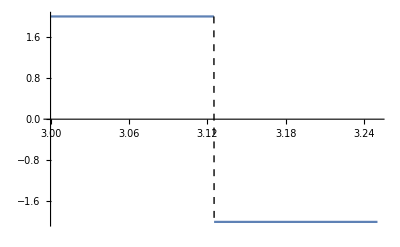

```mathematica
h=Piecewise[{{2^(j/2), (k/(2^j))<x<(1/2+k)/(2^j)}, {-2^(j/2), (1/2+k)/(2^j)<x<(1+k)/(2^j)}}]
h1 = Plot[h,{x,3,13/4}, ExclusionsStyle->Dashed]
```

## Example of Function Approximations

```mathematica
f = E^-x Sin[2 Pi x]
```

ⅇ^-x Sin[2 π x]

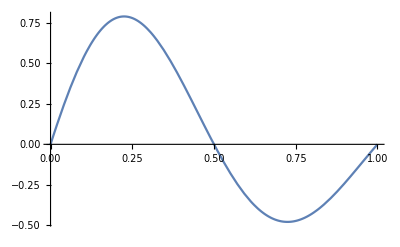

```mathematica
Plot[f,{x,0,1}]
```